((√3)/2 | -1/2
1/2 | (√3)/2)

1

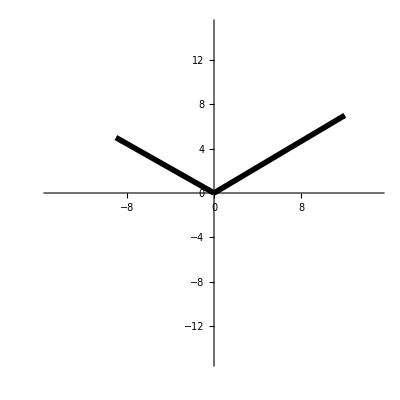

```mathematica
vectorGraphics[p_]:=Graphics[{Arrowheads[.07],Thickness[.01],Black,Arrow[{{0,0},p}]}];
θ=-1/6 Pi;
A={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};
A//MatrixForm
Det@A
p={12,7};
p2 = {-9,5};
g=vectorGraphics@p;
g2=vectorGraphics@p2;
Show[g,g2,PlotRange-> {{-15,15},{-15,15}},Axes-> True,AxesOrigin-> {0,0}]
```

```mathematica
B={A.p,p2};
B//MatrixForm
Det@B//N
```

(-7/2+6 √3 | 6+(7 √3)/2
-9 | 5)

143.021

123